# Simulation on SMWDC ray - tracking

## Using ANAPAW coordinate (only for MWDC-L)

assume there are 6 planes XX' UU' VV’
each cells with size 20 mm X 16 mm
O’ planes are shifted by 5mm
a particle pass throught the MWDC and created signal
	signal constains : 
 	1) # of wire hitted
 	2) hitted wire ID
 	3) the Leading edge of the signal
 by using the drift velocity, we can reconstruct the particle ray.
 the origin of the cooredinate is

```mathematica
(* have to rotate the UU' and VV' plane *)
```

```mathematica
(* initial *)
a=1;
Remove[a];
```

k is alway {x, a , y, b}
Ray is a 3D lines

## Raw Signal Generation

```mathematica
(* a paricle's travaling path *)
(* k = {x0, a, y0, b} *)
(* 3D Ray *)
Ray[k_,z_]:={k[[1]]+k[[2]]z,k[[3]]+k[[4]]z,z}
(* the {x,y} @ z=-40, z=40 *)
Bound[k_]:={Ray[k,-40][[1;;2]],Ray[k,40][[1;;2]]}
(* Normal of Ray *)
NormRay[k_]:=Normalize[(Ray[k,40]-Ray[k,-40])]
```

## MWDC Construction

```mathematica
(* require planeθ *)
n={28,28,22,22,22,22};
sign={1,-1,-1,1,-1,1}; (* L = 1, R = -1 *)
center[d_]:=Table[d/20 Cos[planeθ[i]]+n[[i]]+1/2+sign[[i]]/8,{i,1,6}]
```

```mathematica
center[390.36]//N
```

{47.893,48.143,37.9894,38.2394,37.9894,38.2394}

```mathematica
(*plane Zpos*)
zpos[plane_]:=Switch[plane,
1,-40,
2,-24,
3,-8,
4,8,
5,24,
6,40]
(* plane angle *)
planeθ[plane_]:=Switch[plane,
1,0,
2,0,
3,ArcCos[0.8],
4,ArcCos[0.8],
5,-ArcCos[0.8],
6,-ArcCos[0.8]
]
(* wire direction *)
wdir[plane_]:={-Sin[planeθ[plane]],Cos[planeθ[plane]],0}
cell(*X,Y,Z*)={20,400,16};
firstwirePosition(*mm*)={0,5,18.125,11.875,18.125,11.875}-942.86{1,1,1,1,1,1};
wstart[plane_,i_]:=
{(i-1)cell[[1]]/Cos[planeθ[plane]]+firstwirePosition[[plane]],0,cell[[3]](plane-1)-40}
(* wire ray*)
w[plane_,i_,s_]:=wstart[plane,i]+s wdir[plane]
(* number of wire *)
numWire[plane_]:=Switch[plane,
1,56,
2,56,
3,44,
4,44,
5,44,
6,44
]
(* Hightlight wire cell *)
Highlight[plane_,wire_,lis_]:=If[MemberQ[lis,{plane,wire,__}],0.5,0.1]
```

### chamber geometery drawing: MWDC[k,XYZ,size,α] MWDC2[k,size, α]

```mathematica
MWDC[k_,XYZ_, size_, α_]:=Module[{J},Graphics3D[{
J=HitList[k];
{Black,Arrow[{{0,0,-40},{0,0,100}}]},
{Black,Arrow[{{0,0,-40},{1120,0,-40}}]},
{Black,Arrow[{{0,0,-40},{0,250,-40}}]},
{Red,Arrow[{Ray[k,-70],Ray[k,70]}]},
Table[{Green,Opacity[Highlight[1,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[1,i]+1/2 cell,wstart[1,i]-1/2 cell]},{i,1,numWire[1]}],
Table[{Green,Opacity[Highlight[2,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[2,i]+1/2 cell,wstart[2,i]-1/2 cell]},{i,1,numWire[2]}],
Table[{Yellow,Opacity[Highlight[3,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[3,i]+1/2 cell{1,1/Cos[planeθ[3]],1},wstart[3,i]-1/2 cell{1,1/Cos[planeθ[3]],1}],-ArcSin[wdir[3][[1]]],{0,0,1},wstart[3,i]]},{i,1,numWire[3]}],
Table[{Yellow,Opacity[Highlight[4,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[4,i]+1/2 cell{1,1/Cos[planeθ[4]],1},wstart[4,i]-1/2 cell{1,1/Cos[planeθ[4]],1}],-ArcSin[wdir[4][[1]]],{0,0,1},wstart[4,i]]},{i,1,numWire[4]}],
Table[{Blue,Opacity[Highlight[5,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[5,i]+1/2 cell{1,1/Cos[planeθ[5]],1},wstart[5,i]-1/2 cell{1,1/Cos[planeθ[5]],1}],-ArcSin[wdir[5][[1]]],{0,0,1},wstart[5,i]]},{i,1,numWire[5]}],
Table[{Blue,Opacity[Highlight[6,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[6,i]+1/2 cell{1,1/Cos[planeθ[6]],1},wstart[6,i]-1/2 cell{1,1/Cos[planeθ[6]],1}],-ArcSin[wdir[6][[1]]],{0,0,1},wstart[6,i]]},{i,1,numWire[6]}]
}, ImageSize->size, PlotRange->XYZ]]
MWDC2[k_, size_, α_]:=Graphics3D[{
J=HitList[k];
fp=FirstPlan[J];
Ymin=Min[Ray[k,-60][[2]],Ray[k,60][[2]]]-20;
Ymax=Max[Ray[k,-60][[2]],Ray[k,60][[2]]]+20;
Corner1[plane_]:={-cell[[1]]/2,Ymin/Cos[planeθ[plane]],-cell[[3]]/2};
Corner2[plane_]:={cell[[1]]/2,Ymax/Cos[planeθ[plane]],cell[[3]]/2};
(*Z*){Black,Arrow[{w[J[[1,1]],J[[1,2]],0],w[J[[1,1]],J[[1,2]],0]+{0,0,100}}]},
(*X*){Black,Arrow[{w[J[[1,1]],J[[1,2]],0],w[J[[1,1]],J[[1,2]],0]+{40,0,0}}]},
(*Y*){Black,Arrow[{w[J[[1,1]],J[[1,2]],0],w[J[[1,1]],J[[1,2]],0]+{0,Ray[k,60][[2]]+50,0}}]},
{Red,Thickness[Large ],Arrow[{Ray[k,-60],Ray[k,60]}]},
Table[{Green,Opacity[Highlight[1,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[1,i]+Corner1[1],wstart[1,i]+Corner2[1]]},{i,J[[1,2]]-2,J[[1,2]]+2}],
Table[{Green,Opacity[Highlight[2,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[2,i]+Corner1[2],wstart[2,i]+Corner2[2]]},{i,J[[fp[[2]],2]]-2,J[[fp[[2]],2]]+2}],
Table[{Yellow,Opacity[Highlight[3,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[3,i]+Corner1[3],wstart[3,i]+Corner2[3]],-ArcSin[wdir[3][[1]]],{0,0,1},wstart[3,i]]},{i,J[[fp[[3]],2]]-2,J[[fp[[3]],2]]+2}],
Table[{Yellow,Opacity[Highlight[4,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[4,i]+Corner1[4],wstart[4,i]+Corner2[4]],-ArcSin[wdir[4][[1]]],{0,0,1},wstart[4,i]]},{i,J[[fp[[4]],2]]-2,J[[fp[[4]],2]]+2}],
Table[{Blue,Opacity[Highlight[5,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[5,i]+Corner1[5],wstart[5,i]+Corner2[5]],-ArcSin[wdir[5][[1]]],{0,0,1},wstart[5,i]]},{i,J[[fp[[5]],2]]-2,J[[fp[[5]],2]]+2}],
Table[{Blue,Opacity[Highlight[6,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[6,i]+Corner1[6],wstart[6,i]+Corner2[6]],-ArcSin[wdir[6][[1]]],{0,0,1},wstart[6,i]]},{i,J[[fp[[6]],2]]-2,J[[fp[[6]],2]]+2}],
Table[{Red,Opacity[0.5],Cylinder[{w[J[[i,1]],J[[i,2]],(Ymin-20)/Cos[planeθ[J[[i,1]]]]],w[J[[i,1]],J[[i,2]],(Ymax+20)/Cos[planeθ[J[[i,1]]]]]},Abs[J[[i,5]]]]},{i,1,Length[J]}],
Text[J[[1,2]],w[J[[1,1]],J[[1,2]],0]+{-10,0,0}]
}, ImageSize->size]
```

```mathematica
MWDC[Rayk[1,60,0],{{20*38,20*57},{-200,200},{-50,50}},500,0.2]
```

-Graphics3D-

```mathematica
k={0,0,0,0};
MWDC2[k,500,0.5]
J//TableForm
```

-Graphics3D-

1 | 48 | -40 | 0. | 2.86 | 2.86 | 2.86 | -2.86
2 | 48 | -24 | 0. | -2.14 | 2.14 | 2.14 | 2.14
3 | 38 | -8 | 0.159 | -0.212 | 0.212 | 0.212 | 0.265
4 | 38 | 8 | -3.591 | 4.788 | 4.788 | 4.788 | -5.985
5 | 38 | 24 | -0.159 | -0.212 | 0.212 | 0.212 | 0.265
6 | 38 | 40 | 3.591 | 4.788 | 4.788 | 4.788 | -5.985

### MWDC full drawing

```mathematica
MWDCfull[k_, size_, α_]:=Module[{J},Graphics3D[{
J=HitList[k];
{Black,Arrow[{{0,0,-40},{0,0,100}}]},
{Black,Arrow[{{0,0,-40},{1120,0,-40}}]},
{Black,Arrow[{{0,0,-40},{0,250,-40}}]},
{Blue,
Arrow[{Crystal[1],Crystal[1]+600{-√3,0,1}}],
Arrow[{Crystal[1],Crystal[1]+{0,200,0}}],
Arrow[{Crystal[1],Crystal[1]+200{1,0,√3}}]},
{Red,Arrow[{Ray[k,Crystal[1][[3]]],Ray[k,70]}]},
{Blue,
Arrow[{Crystal[2],Crystal[2]+600{√3,0,1}}],
Arrow[{Crystal[2],Crystal[2]+{0,200,0}}],
Arrow[{Crystal[2],Crystal[2]+200{-1,0,√3}}]},
{Red,Arrow[{Ray[k,Crystal[2][[3]]],Ray[k,70]}]},
Table[{Green,Opacity[Highlight[1,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[1,i]+1/2 cell,wstart[1,i]-1/2 cell]},{i,1,numWire[1]}],
Table[{Green,Opacity[Highlight[2,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[2,i]+1/2 cell,wstart[2,i]-1/2 cell]},{i,1,numWire[2]}],
Table[{Yellow,Opacity[Highlight[3,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[3,i]+1/2 cell{1,1/Cos[planeθ[3]],1},wstart[3,i]-1/2 cell{1,1/Cos[planeθ[3]],1}],-ArcSin[wdir[3][[1]]],{0,0,1},wstart[3,i]]},{i,1,numWire[3]}],
Table[{Yellow,Opacity[Highlight[4,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[4,i]+1/2 cell{1,1/Cos[planeθ[4]],1},wstart[4,i]-1/2 cell{1,1/Cos[planeθ[4]],1}],-ArcSin[wdir[4][[1]]],{0,0,1},wstart[4,i]]},{i,1,numWire[4]}],
Table[{Blue,Opacity[Highlight[5,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[5,i]+1/2 cell{1,1/Cos[planeθ[5]],1},wstart[5,i]-1/2 cell{1,1/Cos[planeθ[5]],1}],-ArcSin[wdir[5][[1]]],{0,0,1},wstart[5,i]]},{i,1,numWire[5]}],
Table[{Blue,Opacity[Highlight[6,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[6,i]+1/2 cell{1,1/Cos[planeθ[6]],1},wstart[6,i]-1/2 cell{1,1/Cos[planeθ[6]],1}],-ArcSin[wdir[6][[1]]],{0,0,1},wstart[6,i]]},{i,1,numWire[6]}]
}, ImageSize->size, PlotRange->All]]
```

```mathematica
MWDCfull[Rayk[1,50,-9],1000,0.1]
```

-Graphics3D-

```mathematica
MWDCfull2[k_, size_, α_]:=Module[{J,fp},Graphics3D[{
J=HitList[k];
fp=LastPlan[J];
{Black,Arrow[{{0,0,0},{0,0,60}}]},
{Black,Arrow[{{0,0,0},{1120,0,0}}]},
{Black,Arrow[{{0,0,0},{0,250,0}}]},
{Blue,
Arrow[{Crystal[1],Crystal[1]+600{-√3,0,1}}],
Arrow[{Crystal[1],Crystal[1]+{0,200,0}}],
Arrow[{Crystal[1],Crystal[1]+200{1,0,√3}}]},
{Red,Arrow[{Ray[k,Crystal[1][[3]]],Ray[k,70]}]},
{Blue,
Arrow[{Crystal[2],Crystal[2]+600{√3,0,1}}],
Arrow[{Crystal[2],Crystal[2]+{0,200,0}}],
Arrow[{Crystal[2],Crystal[2]+200{-1,0,√3}}]},
(*{Red,Arrow[{Ray[k,Crystal[2][[3]]],Ray[k,70]}]},*)
Text[J,{500,0,-400}],
Table[{Green,Opacity[Highlight[1,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[1,i]+1/2 cell,wstart[1,i]-1/2 cell]},{i,J[[fp[[1]],2]]-1,J[[fp[[1]],2]]+1}],
Table[{Green,Opacity[Highlight[2,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[2,i]+1/2 cell,wstart[2,i]-1/2 cell]},{i,J[[fp[[2]],2]]-1,J[[fp[[2]],2]]+1}],
Table[{Yellow,Opacity[Highlight[3,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[3,i]+1/2 cell{1,1/Cos[planeθ[3]],1},wstart[3,i]-1/2 cell{1,1/Cos[planeθ[3]],1}],-ArcSin[wdir[3][[1]]],{0,0,1},wstart[3,i]]},{i,J[[fp[[3]],2]]-1,J[[fp[[3]],2]]+1}],
Table[{Yellow,Opacity[Highlight[4,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[4,i]+1/2 cell{1,1/Cos[planeθ[4]],1},wstart[4,i]-1/2 cell{1,1/Cos[planeθ[4]],1}],-ArcSin[wdir[4][[1]]],{0,0,1},wstart[4,i]]},{i,J[[fp[[4]],2]]-1,J[[fp[[4]],2]]+1}],
Table[{Blue,Opacity[Highlight[5,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[5,i]+1/2 cell{1,1/Cos[planeθ[5]],1},wstart[5,i]-1/2 cell{1,1/Cos[planeθ[5]],1}],-ArcSin[wdir[5][[1]]],{0,0,1},wstart[5,i]]},{i,J[[fp[[5]],2]]-1,J[[fp[[5]],2]]+1}],
Table[{Blue,Opacity[Highlight[6,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[6,i]+1/2 cell{1,1/Cos[planeθ[6]],1},wstart[6,i]-1/2 cell{1,1/Cos[planeθ[6]],1}],-ArcSin[wdir[6][[1]]],{0,0,1},wstart[6,i]]},{i,J[[fp[[6]],2]]-1,J[[fp[[6]],2]]+1}]
}, ImageSize->size, PlotRange->All]]
```

```mathematica
Manipulate[MWDCfull2[Rayk[mwdc,θ,ϕ],700,0.1],{{θ,60},20,70},{{ϕ,0},-15,15},{mwdc,{1,2}}]
```

### MWDC2Rays drawing : MWDC2Rays[k1,k2,size,α], MWDC2RaysFlat[k1,k2,size,α,start plane]

```mathematica
MWDC2Rays[k1_, k2_,size_, α_]:=Graphics3D[{
J1=HitList[k1];
fp1=FirstPlan[J1];
J2=HitList[k2];
fp2=FirstPlan[J2];
Ymin=Min[Ray[k1,-60][[2]],Ray[k1,60][[2]],Ray[k2,60][[2]],Ray[k2,60][[2]]]-20;
Ymax=Max[Ray[k1,-60][[2]],Ray[k1,60][[2]],Ray[k2,60][[2]],Ray[k2,60][[2]]]+20;
Corner1[plane_]:={-cell[[1]]/2,Ymin/Cos[planeθ[plane]],-cell[[3]]/2};
Corner2[plane_]:={cell[[1]]/2,Ymax/Cos[planeθ[plane]],cell[[3]]/2};
(*Z*){Black,Arrow[{w[J1[[1,1]],J1[[1,2]],0],w[J1[[1,1]],J1[[1,2]],0]+{0,0,100}}]},
(*X*){Black,Arrow[{w[J1[[1,1]],J1[[1,2]],0],w[J1[[1,1]],J1[[1,2]],0]+{40,0,0}}]},
(*Y*){Black,Arrow[{w[J1[[1,1]],J1[[1,2]],0],w[J1[[1,1]],J1[[1,2]],0]+{0,Ray[k1,60][[2]]+50,0}}]},
{Red,Thickness[Large ],Arrow[{Ray[k1,-60],Ray[k1,60]}]},
{Orange,Thickness[Large ],Arrow[{Ray[k2,-60],Ray[k2,60]}]},
Table[{Green,Opacity[Highlight[1,i,J1]],EdgeForm[Opacity[α]],Cuboid[wstart[1,i]+Corner1[1],wstart[1,i]+Corner2[1]]},{i,J1[[1,2]]-2,J1[[1,2]]+2}],
Table[{Green,Opacity[Highlight[2,i,J1]],EdgeForm[Opacity[α]],Cuboid[wstart[2,i]+Corner1[2],wstart[2,i]+Corner2[2]]},{i,J1[[fp1[[2]],2]]-2,J1[[fp1[[2]],2]]+2}],
Table[{Yellow,Opacity[Highlight[3,i,J1]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[3,i]+Corner1[3],wstart[3,i]+Corner2[3]],-ArcSin[wdir[3][[1]]],{0,0,1},wstart[3,i]]},{i,J1[[fp1[[3]],2]]-2,J1[[fp1[[3]],2]]+2}],
Table[{Yellow,Opacity[Highlight[4,i,J1]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[4,i]+Corner1[4],wstart[4,i]+Corner2[4]],-ArcSin[wdir[4][[1]]],{0,0,1},wstart[4,i]]},{i,J1[[fp1[[4]],2]]-2,J1[[fp1[[4]],2]]+2}],
Table[{Blue,Opacity[Highlight[5,i,J1]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[5,i]+Corner1[5],wstart[5,i]+Corner2[5]],-ArcSin[wdir[5][[1]]],{0,0,1},wstart[5,i]]},{i,J1[[fp1[[5]],2]]-2,J1[[fp1[[5]],2]]+2}],
Table[{Blue,Opacity[Highlight[6,i,J1]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[6,i]+Corner1[6],wstart[6,i]+Corner2[6]],-ArcSin[wdir[6][[1]]],{0,0,1},wstart[6,i]]},{i,J1[[fp1[[6]],2]]-2,J1[[fp1[[6]],2]]+2}],
Table[{Red,Opacity[0.5],Cylinder[{w[J1[[i,1]],J1[[i,2]],Ymin-20],w[J1[[i,1]],J1[[i,2]],Ymax+20]},Abs[J1[[i,5]]]]},{i,1,Length[J1]}],
Table[{Cyan,Opacity[0.5],Cylinder[{w[J2[[i,1]],J2[[i,2]],Ymin-20],w[J2[[i,1]],J2[[i,2]],Ymax+20]},Abs[J2[[i,5]]]]},{i,1,Length[J2]}]
}, ImageSize->size]
MWDC2RaysFlat[k1_,k2_, size_, α_,plane_]:=(*ImageReflect[*)Graphics[{
J1=HitList[k1];
J2=HitList[k2];
fp1=FirstPlan[J1];
fp2=FirstPlan[J2];
(*Z*){Black,Arrow[{Drop[w[J1[[plane,1]],J1[[plane,2]],0],{2}],Drop[w[J1[[plane,1]],J1[[plane,2]],0],{2}]+{0,30}}]},
(*X*){Black,Arrow[{Drop[w[J1[[plane,1]],J1[[plane,2]],0],{2}],Drop[w[J1[[plane,1]],J1[[plane,2]],0],{2}]+{30,0}}]},
{Red,Thickness[Large ],Arrow[{Drop[Ray[k1,-50],{2}],Drop[Ray[k1,-10],{2}]}]},
{Blue,Thickness[Large ],Arrow[{Drop[Ray[k2,-50],{2}],Drop[Ray[k2,-10],{2}]}]},
Table[{Green,Opacity[0.2],EdgeForm[Opacity[α]],Rectangle[Drop[wstart[plane,i]-1/2 cell/{wdir[plane][[2]],1,1},{2}],Drop[wstart[plane,i]+1/2 cell/{wdir[plane][[2]],1,1},{2}]]},{i,J1[[fp1[[plane]],2]],J1[[fp1[[plane]],2]]+2}],
Table[{Green,Opacity[0.2],,EdgeForm[Opacity[α]],Rectangle[Drop[wstart[plane+1,i]-1/2 cell/{wdir[plane+1][[2]],1,1},{2}],Drop[wstart[plane+1,i]+1/2 cell/{wdir[plane+1][[2]],1,1},{2}]]},{i,J1[[fp1[[plane+1]],2]],J1[[fp1[[plane+1]],2]]+2}],
Table[{Red,
Circle[Drop[w[J1[[i,1]],J1[[i,2]],0],{2}],Abs[{J1[[i,5]]/Cos[planeθ[fp1[[i]]]],J1[[i,5]]}]]},{i,fp1[[plane]],fp1[[plane+1]]+1}],
Table[{Blue,
Circle[Drop[w[J2[[i,1]],J2[[i,2]],0],{2}],Abs[{J2[[i,5]]/Cos[planeθ[fp2[[i]]]],J2[[i,5]]}]]},{i,fp2[[plane]],fp2[[plane+1]]+1}],
Text[{J1[[1,2]],J1[[1,6]]-Crystal[1][[1]]},Drop[w[J1[[1,1]],J1[[1,2]],0]+{-5,0,0},{2}]],
Text[{J1[[fp1[[2]],2]],J1[[fp1[[2]],6]]-Crystal[1][[1]]},Drop[w[J1[[fp1[[2]],1]],J1[[fp1[[2]],2]],0]+{-5,0,0},{2}]]
}, ImageSize->size](*,Left->Right]*)
```

```mathematica
MWDC2Rays[Rayk[1,41,0],Rayk[1,42,4],500,0.1]
```

-Graphics3D-

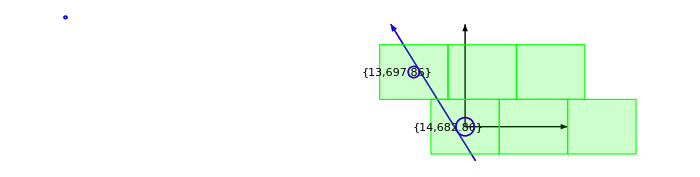

```mathematica
k={-710.8,-0.62,-126.6,-0.09};
MWDC2RaysFlat[k,k,700,1,1]
```

## Signal Construction

```mathematica
MaxDriftLen[plane_]:=Switch[plane,
1,12,
2,12,
3,12,
4,12,
5,12,
6,12
]
DriftLen[k_,plane_,i_]:={s,z,dl}/.Flatten[Solve[w[plane,i,s]+dl Normalize[Cross[wdir[plane],NormRay[k]]]==Ray[k,z],{s,z,dl}]]
(* another method to calculate driftlenght *)
DriftLength[k_,plane_,i_]:=Abs[(wstart[plane,i]-Ray[k,0]).Normalize[Cross[wdir[plane],NormRay[k]]]]
(* general 2 ray distance *)
Distance[ray1_,ray1Norm_,ray2_,ray2Norm_]:=(ray1-ray2).Normalize[Cross[ray1Norm,ray2Norm]]
IncAng[k_]:=Table[ArcCos[1/(√(1+(k[[2]]Cos[planeθ[i]]+k[[4]]Sin[planeθ[i]])^2))],{i,1,6}]
HitList[k_]:= (* plane, wire, z, s, DL, wire Distance *)
Flatten[DeleteCases[Table[If[Abs[DriftLen[k,plane,i][[3]]]<MaxDriftLen[plane],
{plane,i,(plane-1)*cell[[3]]-40,DriftLen[k,plane,i][[1]],DriftLen[k,plane,i][[3]],Distance[wstart[plane,i],wdir[plane],{0,0,0},{0,0,1}],(DriftLen[k,plane,i][[3]])/Cos[IncAng[k][[plane]]]},0]
,{plane,1,6},{i,1,numWire[plane]}]
,0,2]
,1]
CountPlan[Lis_]:=Table[Count[Transpose[Lis][[1]],i],{i,1,6}];
FirstPlan[Lis_]:=Flatten[Table[Position[Lis,{i,__}][[1]],{i,1,6}]];
(* If plane does not exit, use last plane *)
LastPlan[Lis_]:=Table[Total[CountPlan[Lis][[1;;i]]],{i,1,6}];
ReducedFstHitList[k_]:=Module[{J,FstPlan},J=HitList[k];FstPlan=LastPlan[J];Table[J[[i]],{i,FstPlan}]]
ShortedHitList[k_]:=Module[{J,multi,FstPlan},J=HitList[k];multi=CountPlan[J];FstPlan=LastPlan[J];
DeleteCases[Table[If[multi[[i]]==0,0,If[multi[[i]]≠1 ,
If[ J[[FstPlan[[i]],5]]<J[[FstPlan[[i]]-1,5]],J[[FstPlan[[i]]]],J[[FstPlan[[i]]-1]]],
J[[FstPlan[[i]]]]
]],{i,6}],0,1]
]
```

```mathematica
k=Rayk[1,20,-5];
J=HitList[k];
J//TableForm
CountPlan[J]
FirstPlan[J]
LastPlan[J]
ShortedHitList[k]//TableForm
```

1 | 8 | -40 | -36.9193 | 7.76797 | -802.86 | 5.9445
1 | 9 | -40 | -36.5353 | -7.53718 | -782.86 | 5.76788
2 | 7 | -24 | -37.5724 | 8.94724 | -817.86 | 6.84694
2 | 8 | -24 | -37.1884 | -6.35791 | -797.86 | 4.86544
3 | 4 | -8 | -48.1524 | 1.06962 | -679.788 | 0.877773
4 | 4 | 8 | -45.6896 | -3.97021 | -684.788 | 3.25813
5 | 5 | 24 | -45.95 | 5.10123 | -659.788 | 4.27794
5 | 6 | 24 | -56.0539 | -11.671 | -639.788 | 9.78737
6 | 5 | 40 | -49.454 | 0.578546 | -664.788 | 0.485174

{2,2,1,1,2,1}

{1,3,5,6,7,9}

{2,4,5,6,8,9}

1 | 9 | -40 | -36.5353 | -7.53718 | -782.86 | 5.76788
2 | 8 | -24 | -37.1884 | -6.35791 | -797.86 | 4.86544
3 | 4 | -8 | -48.1524 | 1.06962 | -679.788 | 0.877773
4 | 4 | 8 | -45.6896 | -3.97021 | -684.788 | 3.25813
5 | 6 | 24 | -56.0539 | -11.671 | -639.788 | 9.78737
6 | 5 | 40 | -49.454 | 0.578546 | -664.788 | 0.485174

## Drift-Time to Drift-Length Conversion

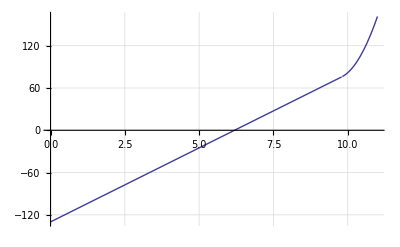

```mathematica
DLcDT[dl_]:=Module[{cut},cut=9.8;Piecewise[{{dl/2,dl<cut},{dl^2+(1/2-2 cut)dl+(cut)^2,dl≥  cut}}] 210/5-130]
Plot[DLcDT[x],{x,0,11},GridLines->Automatic]
```

```mathematica
InverseFunction[DLcDT][50]
```

8.57143

### Drift Time - Drift Length

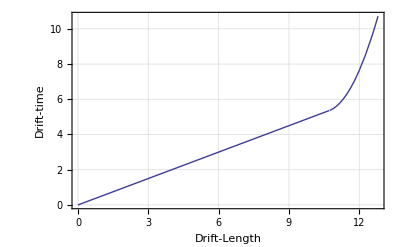

```mathematica
DriftTime[x_]:=Piecewise[{{x/2,x<10.7212},{x^2+(1/2-2 10.7212)x+(10.7212)^2,x≥  10.7212}}]
Plot[DriftTime[x],{x,0,12.8}, Frame->True, FrameLabel->{"Drift-Length","Drift-time"}, GridLines->Automatic]
```

## Target Geometry

```mathematica
Crystal[mwdc_]:=Switch[mwdc,
(*1,{942.86,0,-1400}, Plastics*)
1,{0,0,-982.37},
2,{-390.36+552.5,0,-982.37} (* need to change *)
]
(* norm Ray vector in mwdc frame, {θ,ϕ} = lab angle *)
Rayn[mwdc_,θ_,ϕ_]:=RotationMatrix[(-1)^mwdc π/3,{0,1,0}].{(-1)^(mwdc+1)Sin[θ °]Cos[ϕ °],(-1)^(mwdc+1)Sin[θ °]Sin[ϕ °],Cos[θ °]}
(* Ray from Crystal *)
RayC[mwdc_,θ_,ϕ_,s_]:=Crystal[mwdc]+s Rayn[mwdc,θ,ϕ]
Rayk[mwdc_,θ_,ϕ_]:={
RayC[mwdc,θ,ϕ,s/.Flatten[Solve[RayC[mwdc,θ,ϕ,s][[3]]==0,s],1]][[1]],
Map[(#1[[1]])/(#1[[3]])&,{RayC[mwdc,θ,ϕ,100]-RayC[mwdc,θ,ϕ,0]}][[1]],
RayC[mwdc,θ,ϕ,s/.Flatten[Solve[RayC[mwdc,θ,ϕ,s][[3]]==0,s],1]][[2]],
Map[(#1[[2]])/(#1[[3]])&,{RayC[mwdc,θ,ϕ,100]-RayC[mwdc,θ,ϕ,0]}][[1]]} 
LabAngleShift[mwdc_]:=Switch[mwdc,
1,-30,
2,150
]
LabAngle [mwdc_,plane_,wire_](*right-low corner, wire, left-up corner*):={LabAngleShift[mwdc]+(-1)^(mwdc+1)ArcCos[Normalize[(-(wstart[plane,wire]+{-10,0,-8})+Crystal[mwdc])].{1,0,0}]*180/π, (* corner *)
LabAngleShift[mwdc]+(-1)^(mwdc+1)ArcCos[Normalize[(-(wstart[plane,wire])+Crystal[mwdc])].{1,0,0}]*180/π, (* wire *)LabAngleShift[mwdc]+(-1)^(mwdc+1)ArcCos[Normalize[(-(wstart[plane,wire]+{10,0,8})+Crystal[mwdc])].{1,0,0}]*180/π} (* corner *)
```

```mathematica
PolarAngle[ray_]:=If[ray[[2]]==0 && ray[[1]]==0, {0,0},{ArcTan[ray[[3]],Norm[ray[[1;;2]]]],ArcTan[ray[[1]],ray[[2]]]}]
XY2angle[mwdc_,k_]:=PolarAngle[RotationMatrix[-(-1)^mwdc π/3,{0,1,0}].Normalize[{k[[1]]-Crystal[mwdc][[1]],k[[3]],-Crystal[mwdc][[3]]}]]
```

## ReConstruction - Multi - Demension Regession

### General ; RayTrackingSelf[k, σ, corr,PlaneID]

```mathematica
H[Planeθ_,Zpos_]:=Table[{Cos[Planeθ[[i]]],Cos[Planeθ[[i]]]Zpos[[i]],Sin[Planeθ[[i]]],Sin[Planeθ[[i]]]Zpos[[i]]},{i,1,6}]
H6=H[{0,0,ArcCos[0.8],ArcCos[0.8],-ArcCos[0.8],-ArcCos[0.8]},{-40,-24,-8,8,24,40}];
C6 = Inverse[Transpose[H6].H6]; (* Covariance Matrix *)
G6=C6.Transpose[H6]; (* the inverse matrix *)
P6=H6.G6; (* projection matrix *)
```

```mathematica
(* more general ray matrix *)
Hg[planeID_]:=Table[
{Cos[planeθ[planeID[[i]]]],
Cos[planeθ[planeID[[i]]]]zpos[planeID[[i]]],
Sin[planeθ[planeID[[i]]]],
Sin[planeθ[planeID[[i]]]]zpos[planeID[[i]]]}
,{i,1,Length[planeID]}];
Cg[planeID_]:= Inverse[Transpose[Hg[planeID]].H6[planeID]];
Gg[planeID_]:=Cg[planeID].Transpose[Hg[planeID]];
Pg[planeID_]:=Hg[planeID].Gg[planeID];
```

```mathematica
(* Function of HitList  *)
Binery[n_,digit_]:=If[Length[IntegerDigits[n,2]]<digit, 
Join[ Reverse[IntegerDigits[n,2]],Table[0,{i,1,digit-Length[IntegerDigits[n,2]]}]],
Reverse[IntegerDigits[n,2]]]
PossPos[J_,σ_,corr_,PlaneID_]:=Module[{len,tran,bin},
len=Length[PlaneID];
tran=Transpose[Table[J[[i]],{i,PlaneID}]];
Table[bin=(-1)^Binery[i,len];tran[[6]]+bin (tran[[If[corr==1,7,5]]]+RandomVariate[NormalDistribution[0,σ],len]),{i,0,2^len-1}]
]
RayTrackingSelf[k_,σ_,corr_,PlaneID_]:=Module[{len,hh,PosiYList,SSError,SortedSSError},
J=ShortedHitList[k];
PosiYList=PossPos[J,σ,corr,PlaneID];
len=Length[PosiYList];
hh=Hg[PlaneID];
SSError=Table[{i,LinearModelFit[{hh,PosiYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,len}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
LinearModelFit[{hh,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}][{"BestFitParameters","ParameterErrors","Response"}]
]
```

```mathematica
(*k=Rayk[1,20];*)
k=Rayk[1,20,0];
k={-317.170807,-0.639517069 ,165.639908,-0.118844986};
MWDC2[k,600,0.1];
ShortedHitList[k]//TableForm
planeID={1,2,3,4,5,6};
Estβ=RayTrackingSelf[k,0.0001,0,planeID];
EstβCorr=RayTrackingSelf[k,0.0001,1,planeID];
TableForm[{{"k",k},{"No Corr",Estβ[[1]]},{"Corr",EstβCorr[[1]]},{"",k-Estβ[[1]]},{"",k-EstβCorr[[1]]}},TableDepth->2]
```

1 | 34 | -40 | 170.865 | -7.35475 | -282.86 | -8.73012
2 | 33 | -24 | 168.706 | -3.33815 | -297.86 | -3.9624
3 | 31 | -8 | 214.421 | -8.5541 | -139.788 | -9.90134
4 | 30 | 8 | 202.257 | 4.98657 | -164.788 | 5.77193
5 | 20 | 24 | 201.248 | -3.56928 | -359.788 | -3.89995
6 | 20 | 40 | 197.699 | -5.4408 | -364.788 | -5.94486

k | {-317.171,-0.639517,165.64,-0.118845}
No Corr | {-317.622,-0.686449,166.658,-0.252125}
Corr | {-317.171,-0.639514,165.64,-0.118841}
 | {0.451492,0.0469321,-1.01762,0.13328}
 | {-6.89686×10^-6,-2.7355×10^-6,-0.0000930724,-4.0843×10^-6}

```mathematica
Estβ
```

{{-317.622,-0.686445,166.657,-0.252095},{0.25959,0.00827692,0.411685,0.0278734},{-290.215,-301.198,-148.342,-159.801,-363.357,-370.229}}

### Experiment data process

```mathematica
(* expList = Table[{wpos, dist}] *)
GenExpList[k_,corr_,σ_]:=Module[{J},
J=ShortedHitList[k];
Table[{J[[i,1]],J[[i,6]],J[[i,If[corr==1,7,5]]]++RandomVariate[NormalDistribution[0,σ],6]},{i,1,6}]
]
PossPosExp[explist_]:=Module[{len,tran,bin},
len=Length[explist];tran=Transpose[explist];
Table[bin=(-1)^Binery[i,len];tran[[2]]+bin tran[[3]],{i,0,2^len-1}]]
RayTracking[expList_]:=Module[{planeID,len,PossYList,hh,SSError,SortedSSError},
PossYList=PossPosExp[expList];
len=Length[PossYList];
planeID=Transpose[expList][[1]];
hh=hG[planeID];
SSError=Table[{i,LinearModelFit[{hh,PossYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,len}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
LinearModelFit[{hh,PossYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}][{"BestFitParameters","ParameterErrors","Response","ANOVATable"}]
]
ExpIncAngCorrPosiYList[explist_,β_]:=Module[{CorrDLz,bin,tran,len},
CorrDLz=Table[explist[[i,3]] √(1+(β[[2]]Cos[planeθ[i]]+β[[4]]Sin[planeθ[i]])^2),{i,1,6}];
tran=Transpose[explist];
len=Length[explist];
Table[bin=(-1)^Binery[i,len];tran[[2]]+bin CorrDLz,{i,0,2^len-1}]
]
```

```mathematica
expdata={
{1,-642.86,6.47},
{2,-637.86,5.78},
{3,-519.79,1.28},
{4,-524.79,4.00},
{5,-479.79,6.82},
{6,-484.78,0.48}};
RayTracking[expdata]
estβ[1]=RayTracking[expdata][[1]];
numIter=6;
Monitor[Do[
PosiYList=ExpIncAngCorrPosiYList[expdata,estβ[num]];
SSError=Table[{i,LinearModelFit[{h6,PosiYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,Length[PosiYList]}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
estβ[num+1]=LinearModelFit[{h6,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["BestFitParameters"];
,{num,1,numIter-1}],num]
TableForm[Table[estβ[i],{i,1,numIter}]]
ShortedHitList[estβ[1]]//TableForm
ShortedHitList[estβ[numIter]]//TableForm
MWDC2[estβ[1],500,0.1]
```

{{-631.099,0.104664,-26.5282,-0.0500899},{1.25184,0.0399145,1.9853,0.134416},{-636.39,-632.08,-521.07,-520.79,-486.61,-484.3}, | DF | SS | MS | F-Statistic | P-Value
x0 | 1 | 1.81729×10^6 | 1.81729×10^6 | 926590. | 1.07922×10^-6
a | 1 | 436.376 | 436.376 | 222.497 | 0.00446436
y0 | 1 | 860.781 | 860.781 | 438.891 | 0.00227071
b | 1 | 0.272354 | 0.272354 | 0.138866 | 0.745196
Error | 2 | 3.92253 | 1.96126 |  | 
Total | 6 | 1.81859×10^6 |  |  | }

-631.099 | 0.104664 | -26.5282 | -0.0500899
-631.099 | 0.103816 | -26.5194 | -0.050608
-631.099 | 0.103823 | -26.5192 | -0.0506208
-631.099 | 0.103823 | -26.5192 | -0.0506211
-631.099 | 0.103823 | -26.5192 | -0.0506211
-631.099 | 0.103823 | -26.5192 | -0.0506211

1 | 16 | -40 | -24.4854 | 7.53289 | -642.86 | 7.57403
2 | 16 | -24 | -25.304 | 4.22558 | -637.86 | 4.24866
3 | 12 | -8 | -31.5889 | -1.43582 | -519.788 | -1.43788
4 | 12 | 8 | -36.9526 | 4.4146 | -524.788 | 4.42095
5 | 14 | 24 | -39.4793 | -6.40243 | -479.788 | -6.44375
6 | 14 | 40 | -35.3831 | 0.374399 | -484.788 | 0.376815

1 | 16 | -40 | -24.4548 | 7.56716 | -642.86 | 7.60783
2 | 16 | -24 | -25.2821 | 4.24617 | -637.86 | 4.26899
3 | 12 | -8 | -31.5821 | -1.42243 | -519.788 | -1.4244
4 | 12 | 8 | -36.9452 | 4.41244 | -524.788 | 4.41856
5 | 14 | 24 | -39.495 | -6.41643 | -479.788 | -6.45758
6 | 14 | 40 | -35.4129 | 0.355036 | -484.788 | 0.357313

-Graphics3D-

### Anyplane Ray Tracking For expdata

```mathematica
PossPosExpSelect[explist_,PlaneID_]:=Module[{len,tran,bin},
len=Length[PlaneID];tran=Transpose[Table[explist[[i]],{i,PlaneID}]];
Table[bin=(-1)^Binery[i,len];tran[[2]]+bin tran[[3]],{i,0,2^len-1}]]
RayTrackingSelect[expList_,PlaneID_]:=Module[{len,PossYList,hh,SSError,SortedSSError},
PossYList=PossPosExp2[expList,PlaneID];
len=Length[PossYList];
hh=hG[PlaneID];
SSError=Table[{i,LinearModelFit[{hh,PossYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,len}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
LinearModelFit[{hh,PossYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}][{"BestFitParameters","ParameterErrors","Response"}]
]
```

```mathematica
expdata={{1,-742.860046,7.927},{2,-757.860046,5.18},{3,-619.787964,0.512},{4,-624.787964,5.246},{5,-639.787964,0.692},{6,-644.787964,5.30}};
β6=RayTracking[expdata]
planeID5=Table[Drop[{1,2,3,4,5,6},{i}],{i,1,6}];
Do[
β5[i]=RayTrackingSelect[expdata,planeID5[[i]]]
,{i,1,6}]
TableForm[Table[β5[i][[1]],{i,1,6}]]
TableForm[Table[β5[i][[2]],{i,1,6}]]
TableForm[Table[β5[i][[3]],{i,1,6}]]
```

{{-781.633,-0.771409,0.268567,0.00243022},{0.150813,0.00480861,0.239175,0.0161935},{-750.787,-763.04,-620.3,-630.034,-640.48,-650.088}}

-781.901 | -0.787267 | 1.42479 | -0.0643117
-782.007 | -0.781514 | 1.5624 | -0.0652417
-779.273 | -1.10837 | 30.9338 | -1.58167
-781.447 | -0.766608 | 1.47072 | -0.0199296
-781.496 | -0.768133 | 0.0516731 | 0.011561
-781.489 | -0.767907 | 0.896174 | -0.0958139

0.109274 | 0.0045531 | 0.174 | 0.0117995
0.195133 | 0.00551204 | 0.290879 | 0.0193784
0.0118083 | 0.000391882 | 0.0335375 | 0.00185367
0.0289998 | 0.000916037 | 0.0194626 | 0.00256945
0.0299513 | 0.000890646 | 0.0474447 | 0.00290794
0.022543 | 0.000713596 | 0.03614 | 0.00289985

-763.04 | -619.276 | -630.034 | -640.48 | -650.088
-750.787 | -619.276 | -630.034 | -640.48 | -650.088
-734.933 | -752.68 | -619.542 | -640.48 | -639.488
-750.787 | -763.04 | -619.276 | -640.48 | -650.088
-750.787 | -763.04 | -620.3 | -630.034 | -650.088
-750.787 | -763.04 | -619.276 | -630.034 | -639.096

```mathematica
Y6=h6.β6[[1]]
Do[
Y5[i]=h6.(β5[i][[1]])
,{i,1,6}]
Do[
e5[i]=hG[planeID5[[i]]].(β5[i][[1]])-β5[i][[3]];
e5vs6[i]=Y5[i]-Y6;
,{i,1,6}]
TableForm[Table[{i, Y5[i],Norm[e5[i]],Norm[e5vs6[i]]},{i,1,6}],TableDepth->1]
```

{-750.777,-763.119,-620.22,-630.071,-640.314,-650.211}

{1,{-750.41,-763.006,-619.318,-630.013,-640.565,-650.024},0.120948,1.0304}
{2,{-750.746,-763.25,-619.353,-629.983,-640.608,-649.985},0.192982,0.956766}
{3,{-734.938,-752.672,-590.173,-619.544,-640.483,-639.486},0.0102987,38.584}
{4,{-750.783,-763.049,-619.273,-629.277,-640.472,-650.093},0.0137254,1.25297}
{5,{-750.771,-763.061,-620.305,-630.026,-640.142,-650.085},0.0281157,0.240569}
{6,{-750.773,-763.059,-619.279,-630.028,-639.093,-648.002},0.0250346,2.69436}

### Test of multi-hit

```mathematica
k=Rayk[1,30,0];
J=HitList[k];J//TableForm
```

1 | 21 | -40 | 0. | -1.05445 | -542.86 | -1.21757
2 | 20 | -24 | 0. | 3.93593 | -557.86 | 4.54482
3 | 15 | -8 | -6.02417 | 8.84762 | -459.788 | 9.74577
3 | 16 | -8 | 6.33846 | -9.30921 | -439.788 | -10.2542
4 | 15 | 8 | -4.54679 | 6.6778 | -464.788 | 7.35569
4 | 16 | 8 | 7.81585 | -11.479 | -444.788 | -12.6443
5 | 15 | 24 | -3.11192 | -4.57043 | -459.788 | -5.03439
6 | 14 | 40 | 7.77333 | 11.4166 | -484.788 | 12.5755
6 | 15 | 40 | -4.58931 | -6.74025 | -464.788 | -7.42448

```mathematica
hh=hG[Transpose[J][[1]]];hh//TableForm
Inverse[Transpose[hh].hh].Transpose[hh]
```

1 | -40 | 0 | 0
1 | -24 | 0 | 0
0.8 | -6.4 | 0.6 | -4.8
0.8 | -6.4 | 0.6 | -4.8
0.8 | 6.4 | 0.6 | 4.8
0.8 | 6.4 | 0.6 | 4.8
0.8 | 19.2 | -0.6 | -14.4
0.8 | 32. | -0.6 | -24.
0.8 | 32. | -0.6 | -24.

{{0.157495,0.304193,-0.181522,-0.181522,0.349744,0.349744,0.309848,0.0132988,0.0132988},{-0.0117178,-0.00336326,-0.00644374,-0.00644374,0.0111566,0.0111566,0.00596389,0.0017309,0.0017309},{-0.226902,-0.359661,0.645842,0.645842,-0.0458745,-0.0458745,-0.475112,0.00419015,0.00419015},{-0.0023707,0.0158237,-0.033709,-0.033709,0.0295049,0.0295049,0.0199325,-0.0141703,-0.0141703}}

## 5Plan tracking given 6 plane

```mathematica
(* What is the distribution of Omitted plane and 6PRT, Y5(OmittedPLane,OmittedPlant) - Y6(omittedPlane)
```

```mathematica
k=Rayk[1,40,10]
h6.k
J=ShortedHitList[k];J//TableForm
Transpose[J][[6]]+Transpose[J][[7]]
planeID={1,2,3,4,5,6};
RayTrackingSelf[k,0.5,1,planeID][[3]]
h6.RayTrackingSelf[k,0.5,1,{2,3,4,5,6}][[1]]
```

{-365.951,-0.372519,117.748,0.119861}

{-351.051,-357.011,-220.304,-223.921,-372.288,-378.207}

1 | 31 | -40 | 112.632 | -7.67537 | -342.86 | -8.19063
2 | 30 | -24 | 114.905 | 0.795652 | -357.86 | 0.849066
3 | 27 | -8 | 146.338 | -0.502872 | -219.788 | -0.515566
4 | 27 | 8 | 147.793 | 0.845517 | -224.788 | 0.866859
5 | 20 | 24 | 141.925 | -11.7237 | -359.788 | -12.5002
6 | 19 | 40 | 157.84 | 6.17208 | -384.788 | 6.58086

{-351.051,-357.011,-220.304,-223.921,-372.288,-378.207}

{-350.548,-357.211,-219.675,-223.416,-372.726,-377.69}

{-349.788,-356.282,-219.413,-224.044,-372.545,-378.304}

```mathematica
n=5000;
kList=Module[{θ,ϕ,k},
DeleteCases[Monitor[Table[
θ=ArcCos[2RandomReal[{0.7,0.98}]-1] 180/π;
ϕ=RandomReal[{-20,20}];
k=Rayk[1,θ,ϕ ];
J=ShortedHitList[k];
If[Length[J]≠ 6 || Abs[k[[3]]]≥ 200,
Reject=True; 0,
Reject=False;k
]
,{ii,1,n}],{ii,θ,ϕ}],0]
];
m=Length[kList]
```

3712

```mathematica
plane5ID=Join[Table[Drop[{1,2,3,4,5,6},{i}],{i,1,6}],{{1,2,3,4,5,6}}]
```

{{2,3,4,5,6},{1,3,4,5,6},{1,2,4,5,6},{1,2,3,5,6},{1,2,3,4,6},{1,2,3,4,5},{1,2,3,4,5,6}}

```mathematica
bestkList=Monitor[Table[RayTrackingSelf[kList[[ii]],0.5,1,plane5ID[[j]]],{ii,1,1000},{j,1,7}],{ii,j}];
```

```mathematica
bestkList[[1,1,1,1]]
```

-780.136

```mathematica
Dbestβ1=Table[bestkList[[i,1,1,1]]-bestkList[[i,7,1,1]],{i,1,1000}];
```

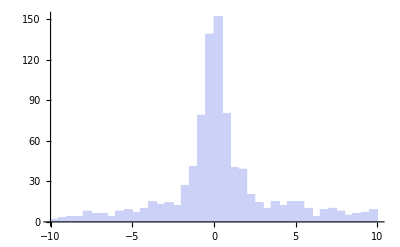

```mathematica
Histogram[Dbestβ1,{-10,10,0.5}]
```

```mathematica
SelBestkList=Select[bestkList,Abs[#[[1,1,1]]-#[[7,1,1]]]>1&];
```

```mathematica
h6.SelBestkList[[2,1,1]]-SelBestkList[[2,7,3]]
```

{-3.02526,-0.0186056,7.1632,13.4232,0.029774,0.335666}

```mathematica
Dbestβ2=Table[bestkList[[i,1,1,2]]-bestkList[[i,7,1,2]],{i,1,1000}];
```

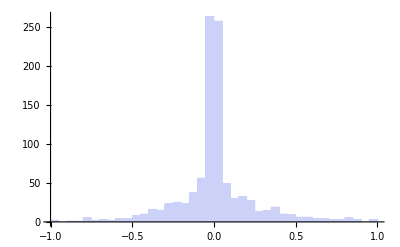

```mathematica
Histogram[Dbestβ2,{-1,1,0.05}]
```

```mathematica
Length[Select[Dbestβ2,Abs[#]>1&]]
```

3

### Import / Export

```mathematica
SetDirectory["/home/goluckyryan/Desktop"]
```

/home/goluckyryan/Desktop

```mathematica
Export["kList.dat",kList]
```

kList.dat

```mathematica
Export["BetaSigmaList.dat",βσList]
```

BetaSigmaList.dat

```mathematica
Export["DLList.dat",DLList]
Export["DLzList.dat",DLzList]
Export["DLz5List.dat",DLz5List]
```

DLList.dat

DLzList.dat

DLz5List.dat

```mathematica
kList=Import["kList.dat"];
DLzList=Import["DLzList.dat"];
DLList=Import["DLList.dat"];
DLz5List=Import["DLz5List.dat"];
βσList=Import["BetaSigmaList.dat"];
```

```mathematica
m=Length[kList]
```

22277

```mathematica
βσList[[1]]//TableForm
```

{-292.0556358070727,
-0.3089516063404643,
30.032902122005403,
0.03282752234854451}
{0.46224093062697497,
0.014738374141422825,
0.7330714718768487,
0.04963302440942192}

```mathematica
StringLength[βσList[[1,1]]]
```

20

```mathematica
βσList1=Monitor[Table[Read[StringToStream[StringTake[βσList[[i,1]],{2,StringLength[βσList[[i,1]]]-1}]],Number],{i,1m}],{i}];
βσList5=Monitor[Table[Read[StringToStream[StringTake[βσList[[i,5]],{2,StringLength[βσList[[i,5]]]-1}]],Number],{i,1m}],{i}];
```

```mathematica
βσList2=Table[Read[StringToStream[βσList[[i,2]]],Number],{i,1,m}];
βσList3=Table[Read[StringToStream[βσList[[i,3]]],Number],{i,1,m}];
βσList4=Table[Read[StringToStream[βσList[[i,4]]],Number],{i,1,m}];
βσList6=Table[Read[StringToStream[βσList[[i,6]]],Number],{i,1,m}];
βσList7=Table[Read[StringToStream[βσList[[i,7]]],Number],{i,1,m}];
βσList8=Table[Read[StringToStream[βσList[[i,8]]],Number],{i,1,m}];
```

```mathematica
βσList=Table[{βσList1[[i]],βσList2[[i]],βσList3[[i]],βσList4[[i]],βσList5[[i]],βσList6[[i]],βσList7[[i]],βσList8[[i]]},{i,1,m}];
```

```mathematica
βσList[[1]]
```

{-292.056,-0.308952,30.0329,0.0328275,0.462241,0.0147384,0.733071,0.049633}

### Resume

```mathematica
J=ShortedHitList[klist[[3]]];J//TableForm
```

1 | 51 | -40 | -66.3788 | 7.26988 | 57.14 | 7.28685
2 | 51 | -24 | -67.5251 | 3.37285 | 62.14 | 3.38072
3 | 39 | -8 | -79.7547 | -8.12105 | 20.212 | -8.12168
4 | 39 | 8 | -85.0568 | -2.92292 | 15.212 | -2.92315
5 | 43 | 24 | -90.6208 | -2.60345 | 100.212 | -2.61566
6 | 43 | 40 | -87.1069 | 3.91762 | 95.212 | 3.936

```mathematica
(* DL *) Transpose[J][[5]]
```

{-9.9478,3.04283,0.110559,4.12309,-11.3507,-8.4616}

```mathematica
(* DLz *) h6.klist[[3]]-Transpose[J][[6]]
(* DLz5-1*) h6.RayTrackingSelf[klist[[3]],0.5,0,{2,3,4,5,6}][[1]]-Transpose[J][[6]]
```

{7.28685,3.38072,-8.12168,-2.92315,-2.61566,3.936}

{7.32307,3.34126,-7.59755,-2.88814,-2.58794,4.33175}

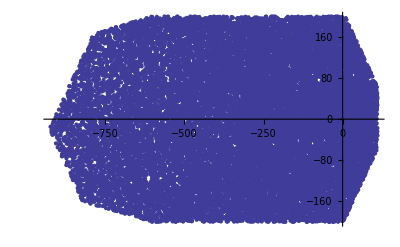

```mathematica
ListPlot[Table[kList[[i,1;;3;;2]],{i,1,m}]]
```

## Systematic Error of Ray Tracking

### Monte Carlo

```mathematica
(* generate a random ray *)
(* get the perpendicular distance between the ray and wire *)
(* use that as Drift-length to calculate the ray parameter *)
(* compare the result *)
```

```mathematica
(* Ray Generation *)
Timing[Error=DeleteCases[Module[
{θ,ϕ,k,J,K,PosiYList,SSError,SortedSSError,bestβ,errβ},
Monitor[Table[
θ=ArcCos[2RandomReal[{0.7,0.98}]-1] 180/π;
ϕ=RandomReal[{-20,20}];
k=Rayk[1,θ,ϕ ];
J=ShortedHitList[k];
If[Length[J]≠ 6 || Abs[k[[3]]]≥ 200,Reject=True; 0,
Reject=False;
PosiYList=PossPos[J,0.3,0,{1,2,3,4,5,6}];
SSError=Table[{i,LinearModelFit[{H6,PosiYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,64}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
(*LinearModelFit[{hh,PosiYList[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["ParameterConfidenceIntervalTable"];*)
bestβ=LinearModelFit[{H6,PosiYList[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["BestFitParameters"];
errβ=LinearModelFit[{H6,PosiYList[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["ParameterErrors"];
Flatten[{θ,ϕ,XY2angle[1,bestβ] 180/π,k,bestβ,errβ,k-bestβ}]
]
,{ii,1,20000}],{ii,θ,ϕ,Reject}]
],0];]
%[[1]]/60
Error[[1]]
m=Length[Error]
```

{3150.97,Null}

52.5162

14751

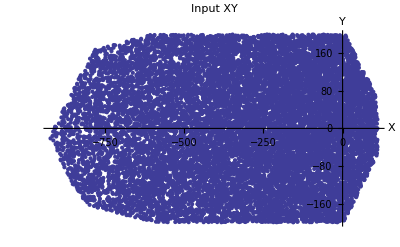

```mathematica
XYList=Table[Error[[i,5;;7;;2]],{i,1,m}];
ListPlot[XYList,PlotLabel->"Input XY",AxesLabel->{"X","Y"},PlotStyle-> PointSize[Small]]
```

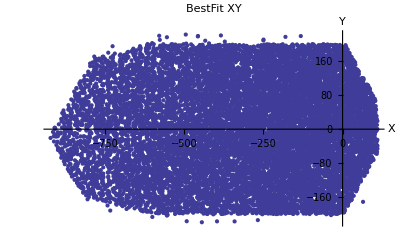

```mathematica
bestXYList=Table[Error[[i,9;;11;;2]],{i,1,m}];
ListPlot[bestXYList,PlotLabel->"BestFit XY",AxesLabel->{"X","Y"},PlotStyle-> PointSize[Small]]
```

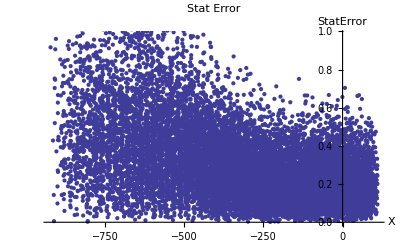

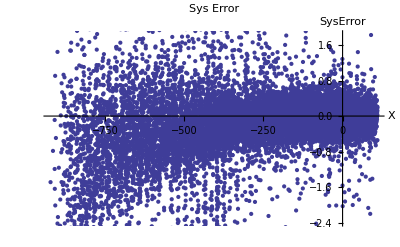

```mathematica
StatErrXX=Table[Error[[i,9;;13;;4]],{i,1,m}];
SysErrXX=Table[Error[[i,9;;17;;8]],{i,1,m}];
ListPlot[StatErrXX,PlotLabel->"Stat Error",AxesLabel->{"X","StatError"}(*, PlotRange->{{500, 700},{0,1}}*)]
ListPlot[SysErrXX,PlotLabel->"Sys Error",AxesLabel->{"X","SysError"}(*, PlotRange->{{500, 700},{-1,1}}*)]
```

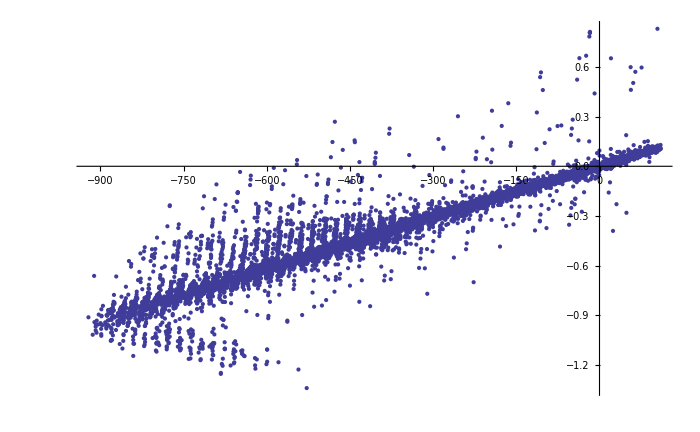

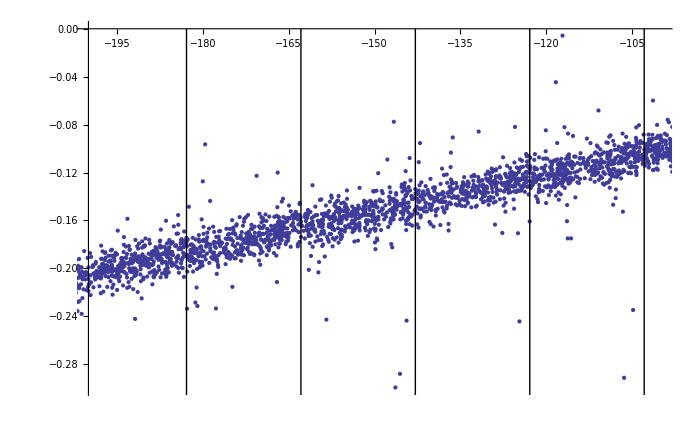

```mathematica
bestXA=Table[Error[[i,9;;10]],{i,1,m}];
ListPlot[bestXA,ImageSize->700,PlotStyle-> PointSize[Small]]
Show[
ListPlot[bestXA,PlotRange->{{-200,-100},{-0.3,0}},PlotStyle-> PointSize[Small]],
Graphics[
Table[
Line[{wstart[1,i][[1;;2]]+{0,-200},wstart[1,i][[1;;2]]}]
,{i,1,56}]
]
]
```

### Iteration

```mathematica
AngCorrPosiYList[β_,J_]:=Module[{bin,Tran,len},
Tran=Transpose[J];
len=Length[J];
Table[bin=(-1)^Binery[i,len];Tran[[6]]+bin Tran[[5]]/Table[Cos[IncAng[β][[j]]],{j,1,6}],{i,0,2^len-1}]
]
```

```mathematica
(* see the convergence progress *)
k=Rayk[1,40,10];
numIter=5;
J=ShortedHitList[k];
J//TableForm
bestβ[1]=RayTrackingSelf[k,0.6,0][[1]];
Monitor[Do[
PosiYList=AngCorrPosiYList[bestβ[num],J];
SSError=Table[{i,LinearModelFit[{H6,PosiYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,Length[PosiYList]}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
bestβ[num+1]=LinearModelFit[{H6,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["BestFitParameters"];
,{num,1,numIter-1}],num]
TableForm[Join[{k},Table[bestβ[i],{i,1,numIter}]]]
```

1 | 31 | -40 | 112.632 | -7.67537 | -342.86 | -8.19063
2 | 30 | -24 | 114.905 | 0.795652 | -357.86 | 0.849066
3 | 27 | -8 | 146.338 | -0.502872 | -219.788 | -0.515566
4 | 27 | 8 | 147.793 | 0.845517 | -224.788 | 0.866859
5 | 20 | 24 | 141.925 | -11.7237 | -359.788 | -12.5002
6 | 19 | 40 | 157.84 | 6.17208 | -384.788 | 6.58086

-365.951 | -0.372519 | 117.748 | 0.119861
-365.951 | -0.372519 | 117.748 | 0.119861
-365.951 | -0.372519 | 117.748 | 0.119861
-365.951 | -0.372519 | 117.748 | 0.119861
-365.951 | -0.372519 | 117.748 | 0.119861
-365.951 | -0.372519 | 117.748 | 0.119861

```mathematica
(* combined together *)
IterateRayTrackingSelf[k_,σ_,numIter_]:=Module[{bestβ,errβ,PosiYList,SSError,SortedSSError},
J=ShortedHitList[k];
bestβ=RayTrackingSelf[k,σ,0][[1]];
Do[
PosiYList=AngCorrPosiYList[bestβ,J];
SSError=Table[{i,LinearModelFit[{H6,PosiYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,Length[PosiYList]}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
bestβ=LinearModelFit[{H6,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["BestFitParameters"];
errβ=LinearModelFit[{H6,PosiYList[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["ParameterErrors"];
,{num,1,numIter-1}];
{bestβ,errβ} (* output *)
]
```

```mathematica
k=Rayk[1,40,10]
IterateRayTrackingSelf[k,1,5]
```

{-365.951,-0.372519,117.748,0.119861}

{{-365.951,-0.372519,117.748,0.119861},{3.81931×10^-13,1.21777×10^-14,6.05708×10^-13,4.10098×10^-14}}

```mathematica
(* Ray Generation *)
Timing[ItaError=DeleteCases[Module[
{θ,ϕ,k,J,bestβ},
Monitor[Table[
θ=ArcCos[2RandomReal[{0.7,0.98}]-1] 180/π;
ϕ=RandomReal[{-10,10}];
k=Rayk[1,θ,ϕ ];
J=ShortedHitList[k];
If[Length[J]≠ 6 || Abs[k[[3]]]≥ 200,Reject=True; 0,
Reject=False;
bestβ=IterateRayTrackingSelf[k,1,5];
Flatten[{θ,ϕ,XY2angle[1,bestβ] 180/π,k,bestβ,k-bestβ}]
]
,{ii,1,20000}],{ii,θ,ϕ,Reject}]
],0];]
%[[1]]/60
m=Length[Error]
```

{12312.2,Null}

205.203

14751

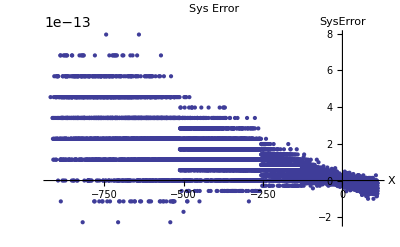

```mathematica
ItaSysErrXX=Table[ItaError[[i,9;;13;;4]],{i,1,m}];
ListPlot[ItaSysErrXX,PlotLabel->"Sys Error",AxesLabel->{"X","SysError"}(*, PlotRange->{{500, 700},{-1,1}}*)]
```

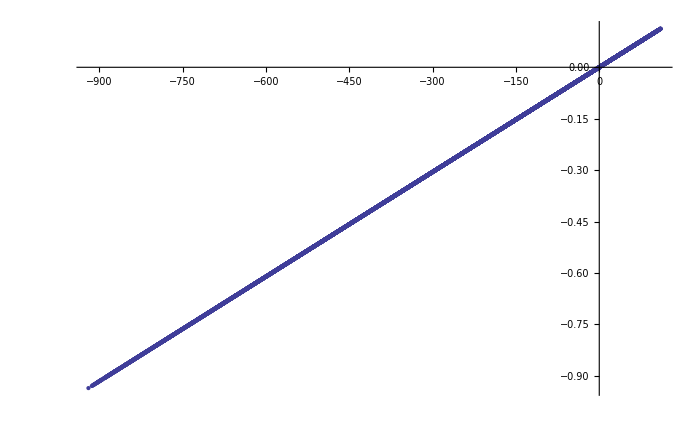

```mathematica
ItabestXA=Table[ItaError[[i,9;;10]],{i,1,m}];
ListPlot[ItabestXA,ImageSize->700,PlotStyle-> PointSize[Small]]
```

## Some Plots

```mathematica
(* Rayk at the end of the cell in X1 *)
MidkX1X2[mwdc_,wire_]:=Rayk[mwdc,LabAngleShift[mwdc]+(-1)^(mwdc+1)ArcCos[Normalize[(-(wstart[1,wire]+{10,0,0})+Crystal[mwdc])].{1,0,0}]*180/π,0]
(* Drift lenght of X1 and X2 *)
DriftX1X2[mwdc_,wire_]:={Abs[DriftLen[MidkX1X2[mwdc,wire],1,wire][[3]]],Abs[DriftLen[MidkX1X2[mwdc,wire],2,wire][[3]]]}

X1X2cell[mwdc_,cell_,shiftAngle_,id1_,id2_]:=MWDC2RaysFlat[
Rayk[mwdc,LabAngle[mwdc,1,cell][[id1]]-shiftAngle,0],Rayk[mwdc,LabAngle[mwdc,2,cell][[id2]],0],500,0.2,1]
X1X2[mwdc_,wire_,color_]:=ListPlot[
Table[
k=Rayk[mwdc,i,0];
{DriftTime[Abs[DriftLen[k,1,wire][[3]]]],DriftTime[Abs[DriftLen[k,2,wire][[3]]]]},{i,LabAngle[mwdc,If[mwdc==1,2,1],wire][[If[mwdc==1,1,3]]],LabAngle[mwdc,If[mwdc==1,1,2],wire][[If[mwdc==1,3,1]]],0.02}]
,Joined->True,PlotRange->{{0,10.7},{0,10.7}},AspectRatio->1,PlotStyle->color]
X1X1p[mwdc_,wire_,color_]:=ListPlot[
Table[
k=Rayk[mwdc,i,0];
{DriftTime[Abs[DriftLen[k,1,wire][[3]]]],DriftTime[Abs[DriftLen[k,1,wire+1][[3]]]]},{i,LabAngle[mwdc,1,wire+1][[1]],LabAngle[mwdc,1,wire][[3]],0.01}]
,Joined->True,PlotRange->{{0,10.7},{0,10.7}},AspectRatio->1,PlotStyle->color]
X1pX2[mwdc_,wire_,color_]:=ListPlot[
Table[
k=Rayk[mwdc,i,0];
{DriftTime[Abs[DriftLen[k,1,wire+1][[3]]]],DriftTime[Abs[DriftLen[k,2,wire][[3]]]]},{i,LabAngle[mwdc,1,If[mwdc==1,wire,wire+1]][[1]],LabAngle[mwdc,2,If[mwdc==1,wire+1,wire]][[3]],0.01}]
,Joined->True,PlotRange->{{0,10.7},{0,10.7}},AspectRatio->1,PlotStyle->color]
(* the X2 Drift Len when X1 hit wire *)
AutoX1X2[mwdc_,cell_]:=DriftLen[Rayk[mwdc,LabAngle[mwdc,1,cell][[2]],0],2,cell][[3]]
AutoX1X2m[mwdc_,cell_]:=DriftLen[Rayk[mwdc,LabAngle[mwdc,1,cell][[2]],0],2,cell-1][[3]]
```

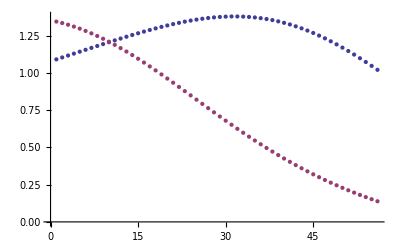

```mathematica
ListPlot[{
Table[LabAngle[1,1,i][[3]]-LabAngle[1,1,i][[1]],{i,56}],
Table[LabAngle[2,1,i][[1]]-LabAngle[2,1,i][[3]],{i,56}]}]
```

```mathematica
FindRoot[LabAngle[1,1,n][[2]]==10,{n,10}]
```

{n→-8.27879}

```mathematica
60-LabAngle[1,1,56][[2]]
```

-9.42277

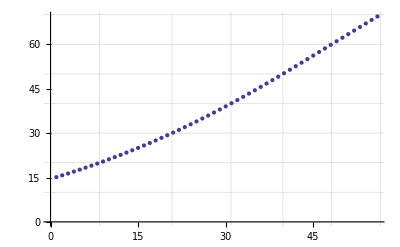

```mathematica
ListPlot[{
Table[{n,LabAngle[1,1,n][[2]]},{n,1,56}]
},GridLines->{{8.417,20.8092,30.9114,39.7951,48.143,56.4909},Table[10 i,{i,0,7}]}]
```

```mathematica
FindRoot[LabAngle[2,1,n][[2]]==70,{n,10}]
```

{n→1.65206}

```mathematica
60-LabAngle[2,1,56][[2]]
```

44.1754

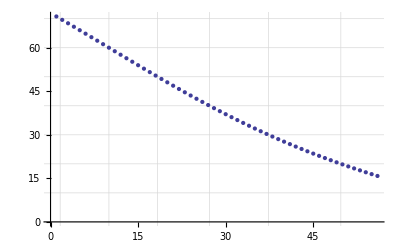

```mathematica
ListPlot[{
Table[{n,LabAngle[2,1,n][[2]]},{n,1,56}]
},GridLines->{{1.65206,10,18.3479,27.2316,37.338,49.7259},Table[10 i,{i,0,7}]}]
```

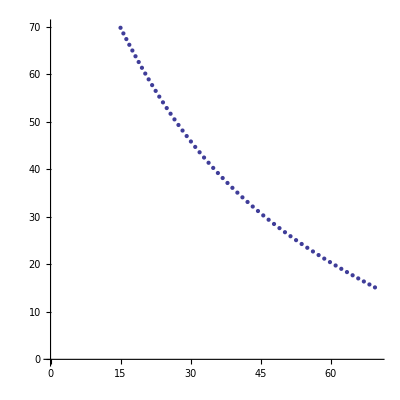

```mathematica
ListPlot[
Table[{LabAngle[1,1,n][[2]],LabAngle[2,1,n][[2]]},{n,1,56}]
,AspectRatio->1,PlotRange->{{0,70},{0,70}}]
```

### L - MWDC

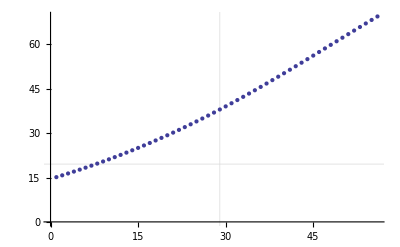

```mathematica
(* incident angle *)
ListPlot[Table[LabAngle[1,1,n][[2]],{n,1,56}],GridLines->{{29},{19.54}}]
```

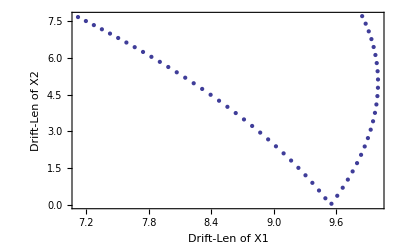

```mathematica
ListPlot[Table[DriftX1X2[1,i],{i,1,56}],Frame->True,FrameLabel->{"Drift-Len of X1","Drift-Len of X2"}]
```

```mathematica
X1X2cell[1,43,0,2,2]
X1X2cell[1,55,0,2,2]
```

-Graphics-

-Graphics-

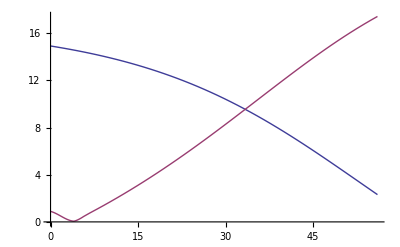

```mathematica
yintL=Table[{n,AutoX1X2[1,n]},{n,0,56,2}];
yintLm=Table[{n,AutoX1X2m[1,n]},{n,0,56,2}];
YintL=Interpolation[Abs[yintL]];
YintLm=Interpolation[Abs[yintLm]];
Plot[{YintL[x],YintLm[x]},{x,0,56},GridLines->{{18.02781807},{√(8^2+10^2)}}]
```

```mathematica
(* experiment data *)
expdataL={
{36,40+130},
{40,20+130},
{45,-10+130},
{47,-25+130},
{50,-50+130}};
expdataLint=Interpolation[expdataL];
```

```mathematica
FindRoot[YintL[x]-YintL[40]/expdataLint[40],{x,20,40}]
```

InterpolatingFunction::dmval: Input value {71.3989} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {63.5004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{x→62.7919}

```mathematica
YintL[40]/expdataLint[40]
```

0.0509319

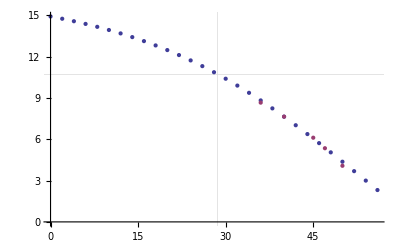

```mathematica
ListPlot[{Abs[yintL],Table[{expdataL[[i,1]],YintL[40]/expdataLint[40] expdataL[[i,2]]},{i,1,5}]},Joined->False, GridLines->{{28.6},{10.7}}]
```

### Plot

```mathematica
LabAngle[1,1,33][[2]]
60-LabAngle[1,1,33][[2]]
X1X2cell[1,33,0,2,2]
```

42.2629

17.7371

-Graphics-

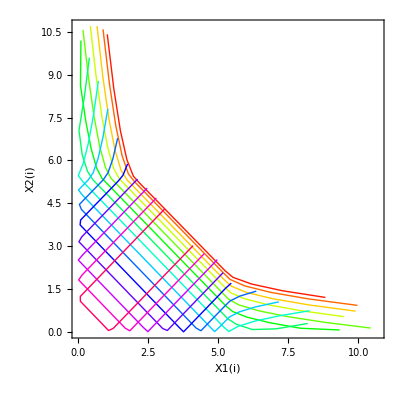

```mathematica
Show[Table[X1X2[1,i,Hue[i/60]],{i,{1, 4,8,12,16,20,24,28,32,36,40,44,48,52,56}}],Frame->True,FrameLabel->{"X1(i)","X2(i)"}]
```

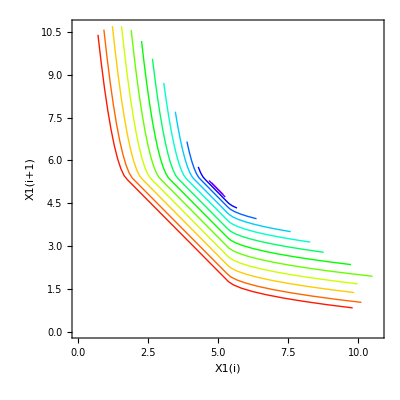

```mathematica
Show[Table[X1X1p[1,i,Hue[i/60]],{i,{1,4,8,12,16,20,24,28,32,36,40,44,45}}],Frame->True,FrameLabel->{"X1(i)","X1(i+1)"}]
```

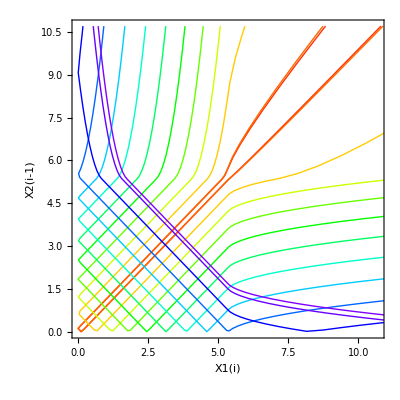

```mathematica
Show[Table[X1pX2[1,i,Hue[i/60]],{i,{2,4,8,12,16,20,24,28,32,36,40,44,45}}],Frame->True,FrameLabel->{"X1(i)","X2(i-1)"}]
```

### MWDC - R

```mathematica
LabAngle[2,1,10][[2]]
60-LabAngle[2,1,10][[2]]
X1X2cell[2,10,0,2,2]
```

60.

0.

-Graphics-

```mathematica
yintR=Table[{n,RAutoX1X2[n]},{n,1,56,1}];
```

```mathematica
Sort[Abs[yintR],#1[[2]]>#2[[2]]&][[-1]]
```

{25,0.0660956}

```mathematica
yintRdata=Map[#-{0,-130}&,{
{5,0},
{8,-25},
{12,-50},
{15,-60},
{20,-105},
{22,-110},
{28,-110},
{31,-90},
{32,-82},
{37,-60},
{39,-45},
{43,-30},
{47,-20},
{49,-10},
{52,0},
{56,20}}];
```

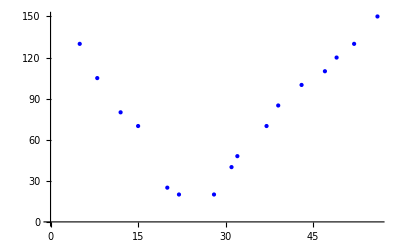

```mathematica
ListPlot[yintRdata,PlotStyle->{ Blue}]
```

```mathematica
yintR[[43,2]]/yintRdata[[12,2]]
```

0.0504738

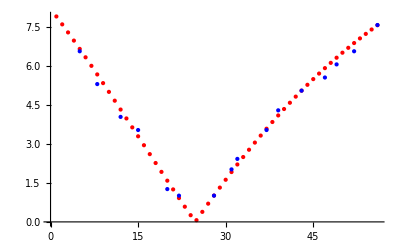

```mathematica
ListPlot[{Abs[yintR],Map[#*{1,yintR[[43,2]]/yintRdata[[12,2]]}&,yintRdata]},PlotStyle->{Red, Blue}]
```

### Plot

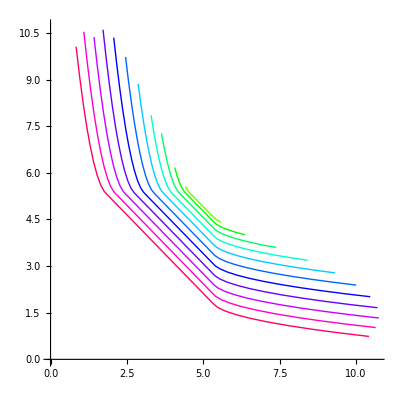

```mathematica
Show[Table[X1X1p[2,i,Hue[i/60]],{i,{16,20,24,28,32,36,40,44,48,52,56}}]]
```

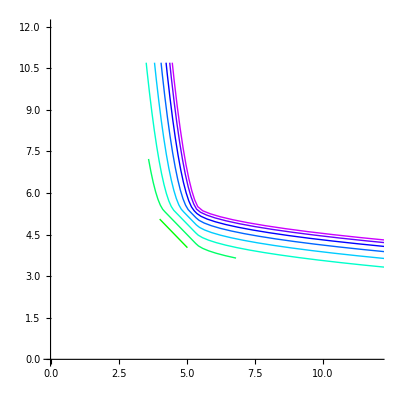

```mathematica
Show[Table[X1pX2[2,i,Hue[i/60]],{i,{20,24,28,32,36,40,44,48}}],PlotRange->{{0,12},{0,12}}]
```

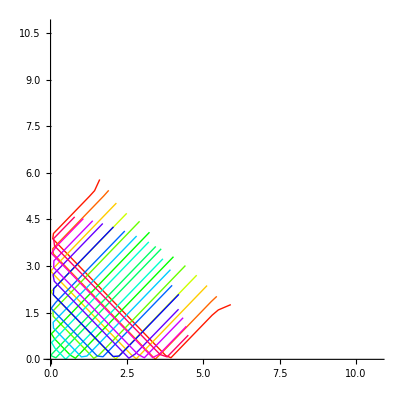

```mathematica
Show[Table[X1X2[2,i,Hue[i/60]],{i,{1,4,8,12,16,20,24,28,32,36,40,44,48,52,56}}]]
```

## PP elastics

```mathematica
mp=938.27203;
T1[T_,α_ ]:=T Cos[α °/2]^2
T2[T_,α_]:=T Sin[α °/2]^2
θ1[T_,α_(* deg *)](* deg *):=ArcTan[Sqrt[T (2 mp+T)] Cos[α °/2]^2,(Sqrt[mp T] Sin[α °])/Sqrt[2]] 180/π
θ2[T_,α_(* deg *)](* deg *):=ArcTan[Sqrt[T (2 mp+T)] Sin[α °/2]^2,-((Sqrt[mp T] Sin[α °])/Sqrt[2])] 180/π
Einc[m_,ToF_ (*ns *),l_]:=With[{c=0.299792458},(m (c ToF √(c^2 ToF^2-l^2)-(c^2 ToF^2-l^2)))/(c^2 ToF^2-l^2)]
ToF[m_,Ein_,l_]:=With[{c=299792458},(l(m+Ein))/(c √(2m Ein+Ein^2))10^9](*ns*)
```

```mathematica
flL[α_]:=Norm[Ray[Rayk[1,θ1[260,α],0],200]-Crystal[1]] (* flight lenght *)
ToFTplL[α_]:=(flL[α](mp +T1[260,α]))/(299792458 √(2mp T1[260,α]+T1[260,α]^2))10^6 (* ns *)
flR[α_]:=Norm[Ray[Rayk[2,-θ2[260,α],0],200]-Crystal[2]] (* flight lenght *)
ToFTplR[α_]:=(flR[α](mp +T2[260,α]))/(299792458 √(2mp T2[260,α]+T2[260,α]^2))10^6 (* ns *)
```

```mathematica
(* Given Lab angle and find the ToF *)
FindRoot[θ1[260,α1]==70,{α1,50}]
ToFTplL[α1]/.%
```

{α1→142.33}

17.0867

```mathematica
(* Given ToF and find the lab angle *)
FindRoot[ToFTplL[α1]==8,{α1,100}]
θ1[260,α1]/.%
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{α1→67.7271}

32.1656

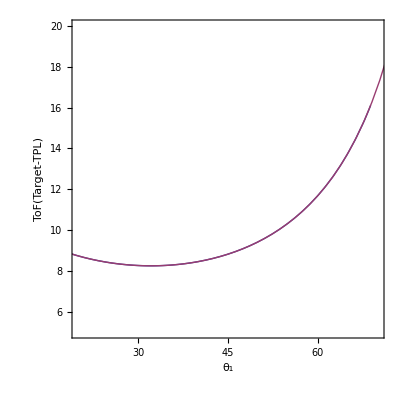

```mathematica
ParametricPlot[{{θ1[260,α],ToFTplL[α]},{-θ2[260,α],ToFTplR[α]}},{α,20,140},AspectRatio-> 1, PlotRange-> {{20,70},{5, 20}},Frame->True, FrameLabel-> {"θ_1","ToF(Target-TPL)"}]
```

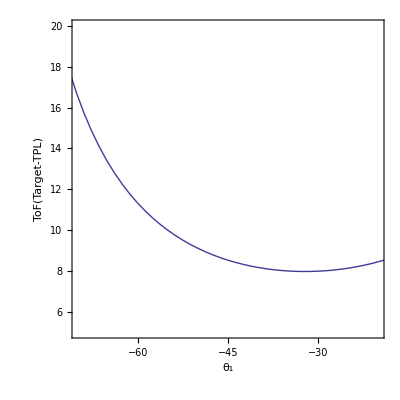

```mathematica
ParametricPlot[{{θ2[260,α],ToFTplR[α]}},{α,20,140},AspectRatio-> 1, PlotRange-> {{-70,-20},{5, 20}},Frame->True, FrameLabel-> {"θ_1","ToF(Target-TPL)"}]
```

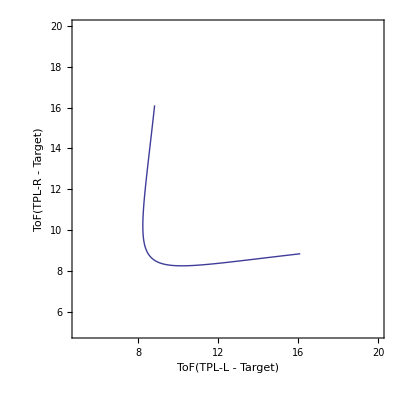

```mathematica
ParametricPlot[{ToFTplL[α],ToFTplR[α]},{α,40,140},AspectRatio-> 1, PlotRange-> {{5,20},{5, 20}},Frame->True, FrameLabel-> {"ToF(TPL-L - Target)","ToF(TPL-R - Target)"}]
```

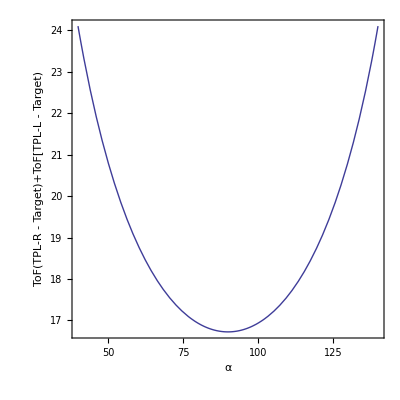

```mathematica
Plot[ToFTplL[α]+ToFTplR[α],{α,40,140},AspectRatio-> 1, Frame->True, FrameLabel-> {"α","ToF(TPL-R - Target)+ToF[TPL-L - Target)"}]
```

```mathematica
(* Timing of Plastics *)
```

```mathematica
F3[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i],{i,0,10}]
FH9[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i-394.574],{i,0,10}]
Tgt[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i-451.7844],{i,0,10}]
SO[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i-463.046],{i,0,10}]
timingTpl=Table[ToFTplL[RandomReal[{42,142}]],{i,0,10}];
PLL[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i-451.7844-timingTpl[[i+1]]],{i,0,10}]
```

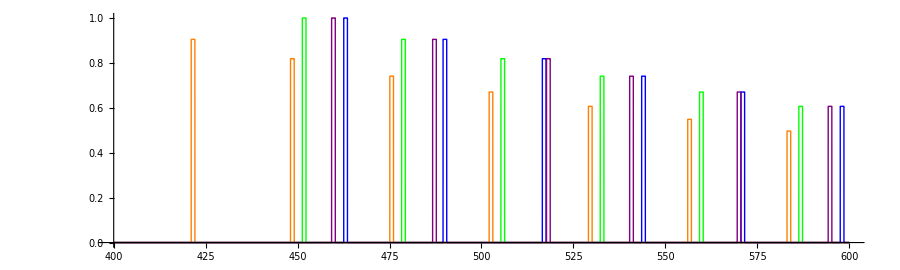

```mathematica
Plot[{F3[t],FH9[t],Tgt[t],SO[t],PLL[t]},{t,400,600},PlotPoints->400,AspectRatio->0.3,ImageSize->900,PlotStyle->{ Red,Orange, Green, Blue,Purple}]
```

```mathematica
θ1[260,90 ]
Rayk[1,θ1[260,90]]
HitList[Rayk[1,θ1[260,90]]][[1,2]]
```

43.1427

{655.949,0,631.708,0}

34

```mathematica
MWDC2RaysFlat[Rayk[1,θ1[260,90 ]],Rayk[1,θ1[260,91 ]],500, 0.1,1]
```

-Graphics-

```mathematica
MWDC2RaysFlat[Rayk[2,-θ2[260,90 ]],Rayk[2,-θ2[260,91 ]],500, 0.1,1]
```

-Graphics-

```mathematica
(* simulate MWDC L R ID *)
```

```mathematica
{HitList[Rayk[1,θ1[260,36]]][[1,2]],HitList[Rayk[2,-θ2[260,36]]][[1,2]]}
{HitList[Rayk[1,θ1[260,142]]][[1,2]],HitList[Rayk[2,-θ2[260,142]]][[1,2]]}
```

{4,1}

{56,53}

```mathematica
hist=Table[{HitList[Rayk[1,θ1[260,α]]][[1,2]],HitList[Rayk[2,-θ2[260,α]]][[1,2]]},{α,36,140,0.1}];
```

```mathematica
HistogramList[Transpose[hist][[1]],56]
```

{{4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.},{11,14,14,15,14,16,15,15,16,17,16,17,17,18,17,18,19,19,19,19,20,19,21,20,21,21,21,22,21,22,23,22,23,22,23,23,23,24,23,23,24,23,24,23,24,23,23,23,23,23,23,22}}

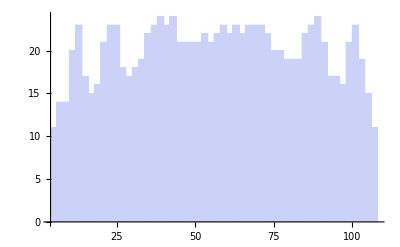

```mathematica
Histogram[Map[Total[#1]&,hist,{1}],56]
```

```mathematica
hist[[1]]
```

{4,1}

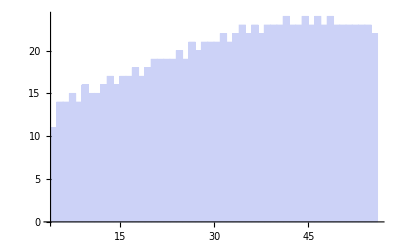

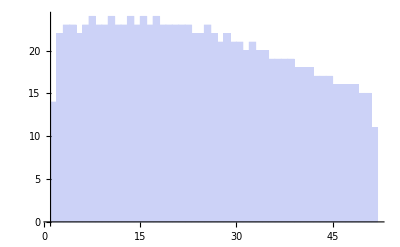

```mathematica
Histogram[Transpose[hist][[1]],56]
Histogram[Transpose[hist][[2]],56]
```

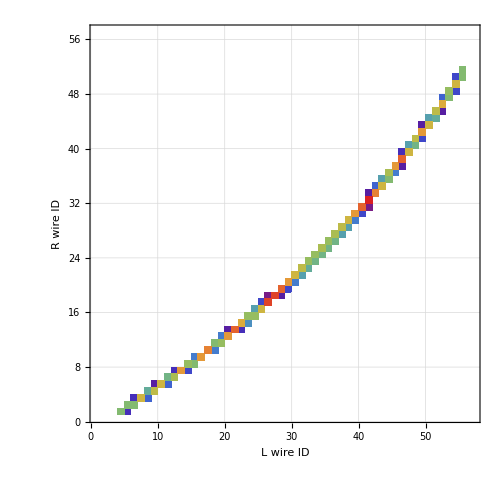

```mathematica
DensityHistogram[hist,56,GridLines->Automatic,PlotRange->{{1,57},{1,57}},ImageSize->500,Frame-> True,FrameLabel->{"L wire ID","R wire ID"},ColorFunction->"Rainbow"]
```

```mathematica
{Rayk[1,θ1[260,36]][[1]],Rayk[2,-θ2[260,36]][[1]]}
{Rayk[1,θ1[260,140]][[1]],Rayk[2,-θ2[260,140]][[1]]}
```

{57.9082,-1.97202}

{1089.03,1007.91}

```mathematica
histXLR=Table[{Rayk[1,θ1[260,α]][[1]],Rayk[2,-θ2[260,α]][[1]]},{α,36,140,0.1}];
```

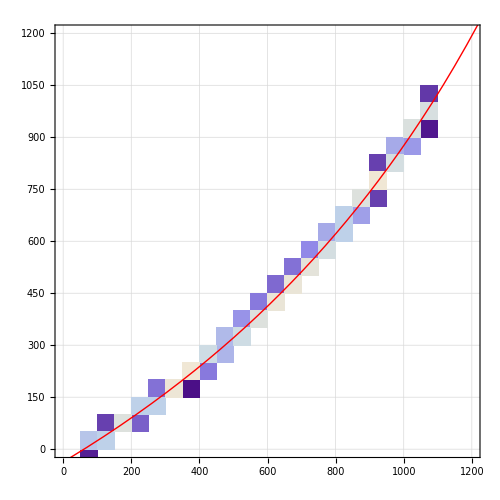

```mathematica
Show[DensityHistogram[histXLR,20,GridLines->Automatic,PlotRange->{{0,1200},{0,1200}},ImageSize->500],
ParametricPlot[{Rayk[1,θ1[260,α]][[1]],Rayk[2,-θ2[260,α]][[1]]},{α,0,180},PlotStyle->Red]]
```